# Zestaw 3

## Zadanie 1. Granice ciągów, Limit, DiscreteLimit, Plot, DiscretePlot

```mathematica
?Limit
```

### Policz granice następujących ciągów:

#### 1)

```mathematica
f[a_, n_] := (1 + a/n)^n
```

```mathematica
Limit[f[a, n], n -> Infinity]
```

ⅇ^a

#### 2)

```mathematica
f[n_] := n Sin[1/n]
```

```mathematica
Limit[f[n], n -> Infinity]
```

1

#### 3)

```mathematica
f[n_] := n Log[1 + 1/n]
```

```mathematica
Limit[f[n], n -> Infinity]
```

1

#### 4)

```mathematica
f[n_] := Sin[n]Log[1 + 1/n]
```

```mathematica
Limit[f[n], n -> Infinity]
```

0

#### 5)

```mathematica
f[n_] := E^n / n
```

```mathematica
Limit[f[n], n -> Infinity]
```

∞

#### 6)

```mathematica
f[n_] := (-1)^n * E^n / n
```

```mathematica
Limit[f[n], n -> Infinity]
```

ComplexInfinity

#### 7)

```mathematica
f[n_] := Sin[n] * E^n / n
```

```mathematica
Limit[f[n], n -> Infinity]
```

Indeterminate

#### 8)

```mathematica
f[n_] := Sin[n * Pi] E^n / n
```

```mathematica
Limit[f[n], n -> Infinity]
```

Indeterminate

```mathematica
?DiscreteLimit
```

```mathematica
DiscreteLimit[f[n], n -> Infinity]
```

0

#### 9)

```mathematica
f[n_] := Sum[1/k, {k, 1, n}] - Log[n]
```

```mathematica
Limit[f[n], n -> Infinity]
```

EulerGamma

Ciekawostka:
Szukana granica w 9) to tzw. stała Eulera-Mascheroniego, 𝜸, do tej pory nie wiadomo, czy stała 𝜸 jest liczbą wymierną, czy niewymierną.

### Jak należy interpretować wyniki ComplexInfinity, Indeterminate?

ComplexInfinity -  lub

Indeterminate - Granica prawdopodobnie nie istnieje

### Czy w powyższych przykładach jest różnica między użyciem funkcji Limit, a funkcji DiscreteLimit?

Tak, dla 8)

### Narysuj ciąg (funkcję)

Narysuj ciąg (funkcję)  korzystając z funkcji Plot w zakresie .

```mathematica
?Plot
```

```mathematica
f[n_] := Sin[n * Pi] * E^n / n
```

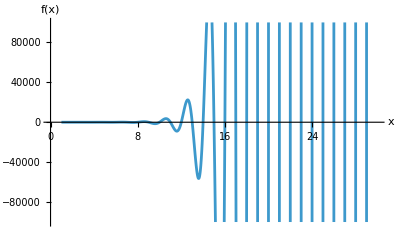

```mathematica
Plot[
f[n],
{n, 1, 30},
AxesLabel->{"x","f(x)"},
PlotRange->{-100000, 100000}
]
```

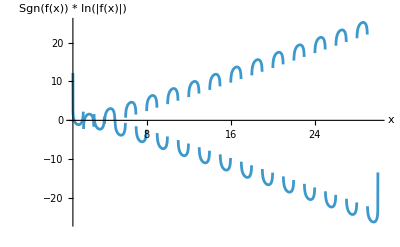

```mathematica
Plot[
Sign[f[n]] * Log[Abs[f[n]]],
{n, 1, 30},
AxesLabel->{"x","Sgn(f(x)) * ln(|f(x)|)"}
]
```

Następnie narysuj ten sam ciąg korzystając z DiscretePlot.

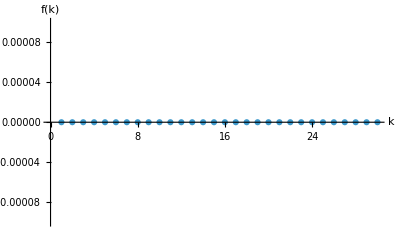

```mathematica
DiscretePlot[
f[n],
{n, 1, 30},
AxesLabel->{"k","f(k)"},
PlotRange->{-0.0001, 0.0001}
]
```

## Zadanie 2. Szeregi liczbowe, Sum

Rozważ płaski ekran ustawiony w punkcie , na który pada światło od ciągu  punktowych źródeł światła umieszczonych na osi  w odległościach   od ekranu.
Każde ze świateł świeci z taką samą mocą, a natężenie światła padającego na ekran od źródła w odległości  wynosi  .
Jakie będzie całkowite natężenie światła padającego na ekran dla ?

```mathematica
?Sum
```

```mathematica
f[n_] := 1 / n^2
```

```mathematica
Sum[f[n], {n, 1, Infinity}]
```

π^2/6

Ciekawostka:
Sumę szeregu, który jest rozwiązaniem tego zadania można wyznaczyć również geometrycznie, https://www.youtube.com/watch?v=d-o3eB9sfls (17 min)

## Zadanie 3. Szeregi liczbowe, Sum, ListPlot, ListLogPlot

Policz granicę następującego ciągu , którego elementami są sumy szeregów.

```mathematica
S[k_] := Sum[1 / n^k, {n, 1, Infinity}]
```

Najpierw sprawdź jak zmienia się  dla  w zakresie .
Wynik zapisz w postaci listy

```mathematica
GetSk[kMax_] := Map[k |-> {k, S[k]}, Range[2, kMax]]
```

Następnie:

### 1) Wypisz sk dla

```mathematica
kMax=20;
sk = GetSk[kMax]
```

{{2,π^2/6},{3,Zeta[3]},{4,π^4/90},{5,Zeta[5]},{6,π^6/945},{7,Zeta[7]},{8,π^8/9450},{9,Zeta[9]},{10,π^10/93555},{11,Zeta[11]},{12,(691 π^12)/638512875},{13,Zeta[13]},{14,(2 π^14)/18243225},{15,Zeta[15]},{16,(3617 π^16)/325641566250},{17,Zeta[17]},{18,(43867 π^18)/38979295480125},{19,Zeta[19]},{20,(174611 π^20)/1531329465290625}}

Jakie wartości przyjmują elementy tej listy dla parzystych ?

```mathematica
sk[[;; ;; 2]]
```

{{2,π^2/6},{4,π^4/90},{6,π^6/945},{8,π^8/9450},{10,π^10/93555},{12,(691 π^12)/638512875},{14,(2 π^14)/18243225},{16,(3617 π^16)/325641566250},{18,(43867 π^18)/38979295480125},{20,(174611 π^20)/1531329465290625}}

### 2) Przedstaw na wykresie korzystając z funkcji ListPlot wartości sk dla

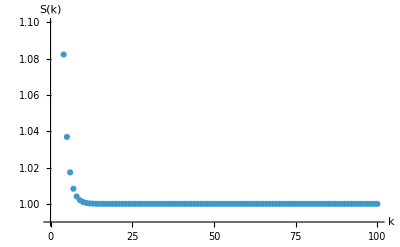

```mathematica
kMax=100;
sk = GetSk[kMax];
ListPlot[
sk,
AxesLabel->{"k","S(k)"},
PlotRange->{0.99, 1.1}
]
```

### 3) Utwórz listę dla

```mathematica
kMax=100;
sk1 = Map[k |-> {k, S[k] - 1}, Range[2, kMax]]
```

### 4) Przedstaw listę sk1 na wykresie ListLogPlot

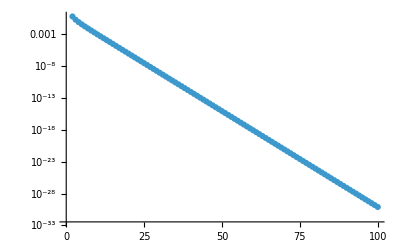

```mathematica
ListLogPlot[sk1]
```

Co sugeruje ten wykres?

Odp.:

Jaka jest granica ciągu  dla ?

```mathematica
Limit[S[k], k -> Infinity]
```

1

Wskazówka:
Jak zachowuje się wartość  przy zwiększaniu . Dlaczego by utworzyć sk1  odjęliśmy wartość 1? Sprawdź wynik działania Limit[Zeta[𝑛], 𝑛→∞].

```mathematica
Limit[Zeta[𝑛], 𝑛 -> Infinity]
```

1

## Zadanie 4. Szeregi liczbowe, SumConvergence, Sum, FullSimplify

Sprawdź czy szereg

jest zbieżny dla  ? Użyj funkcji SumConvergence.

```mathematica
f[k_] := (4/(8k+1) - 2/(8k+4) - 1/(8k+5) - 1/(8k+6)) * 16^(-k)
```

```mathematica
?SumConvergence
```

```mathematica
SumConvergence[f[k], k]
```

True

Policz granicę  korzystając z Sum. Wypisz tę wartość numerycznie

```mathematica
S[n_] := Sum[f[k], {k, 0, n}]
```

```mathematica
limit =Limit[S[n], n->Infinity];
N[limit]
```

lim_(n→∞) -0.0666667 2.^(-7.-4. n) (5.13951 2.^(6.+4. n)+3.07504 2.^(7.+4. n)+3.83119 2.^(8.+4. n)-15.1078 2.^(9.+4. n)+60. LerchPhi[0.0625,1.,1.125+n]-30. LerchPhi[0.0625,1.,1.5+n]-15. LerchPhi[0.0625,1.,1.625+n]-15. LerchPhi[0.0625,1.,1.75+n])

Wynik działania funkcji Sum uprość przy pomocy FullSimplify.

```mathematica
FullSimplify[limit]
```

lim_(n→∞) 2^(-7-4 n) (2^(7+4 n) π-4 LerchPhi[1/16,1,9/8+n]+2 LerchPhi[1/16,1,3/2+n]+LerchPhi[1/16,1,13/8+n]+LerchPhi[1/16,1,7/4+n])

Ciekawostka: 
Jest to tak zwany szereg Bailey-Borwein-Plouffe, został odkryty w 1995 przy pomocy algorytmu PSQL, zaimplementowany w bazie szesnastkowej pozwala obliczać dalekie cyfry rozwinięcia liczby  bez obliczania poprzedzających cyfr.
Więcej informacji: https://observablehq.com/@rreusser/computing-with-the-bailey-borwein-plouffe-formula

## Zadanie 5. Błądzenie przypadkowe w 1D, Module, RandomChoice, Accumulate, Series oraz inne

Zdefiniuj proces, w którym kulka porusza się po osi liczb całkowitych, wykonując skoki w lewo () albo w prawo () z takim samym prawdopodobieństwem .
Jeśli kulka zaczyna błądzenie w punkcie , to jakie jest prawdopodobieństwo , że po dokładnie  skokach znowu znajdzie się w położeniu początkowym?
Dla ustalenia uwagi, rozwiąż dla  skoków.

Zacznij od zdefiniowania własnej funkcji losującej serię  skoków:

```mathematica
getSteps[n_]:=RandomChoice[{−1,1}, n]
```

gdzie −1 odpowiada skokowi w lewo, a +1 skokowi w prawo.

Następnie zdefiniuj funkcję zwracającą pozycję kulki po 1, 2, … 𝑛 skokach:

```mathematica
getWalk[n_]:=Module[
{steps,walk},
steps=getSteps[n];
walk=Accumulate[steps];
walk
]
```

Sprawdź działanie funkcji getWalk przedstawiając jej wynik na wykresie.

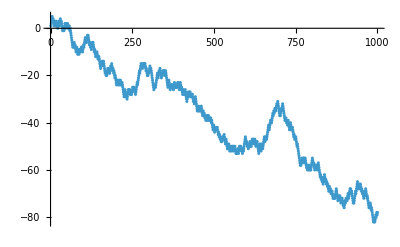

```mathematica
ListPlot[getWalk[1000]]
```

Następnie:

### 1) Oszacuj prawdopodobieństwo numerycznie

Przykładowo wygeneruj  niezależnych błądzeń losowych, sprawdź w ilu z tych błądzeń, , kulka kończyła błądzenie w położeniu .

```mathematica
n = 1000;
```

```mathematica
Experiment := Module[
{walkResults, walksFinishedAtZero},
walkResults = Table[Last[getWalk[n]], 1000];
walksFinishedAtZero = Count[walkResults, 0];
walksFinishedAtZero
];
walksFinishedAtZero = Experiment
```

20

Oszacowanie na  to .

```mathematica
PercentForm[N[walksFinishedAtZero / n]]
```

2%

### 2) Potraktuj punkt 1) jako pojedynczy eksperyment

Wykonaj teraz ten eksperyment  razy.

```mathematica
experimentResults = Table[Experiment / n, 100]
```

{31/1000,7/250,19/1000,31/1000,19/1000,7/250,9/500,21/1000,23/1000,9/250,17/1000,21/1000,11/500,27/1000,23/1000,9/500,3/125,33/1000,13/500,3/125,9/500,7/250,19/1000,3/100,9/500,17/1000,11/500,11/500,23/1000,13/500,13/1000,7/250,13/500,13/500,21/1000,1/40,29/1000,13/500,4/125,3/125,19/1000,4/125,11/500,21/1000,19/1000,11/500,7/250,21/1000,21/1000,17/500,9/500,27/1000,13/500,13/500,1/50,29/1000,17/1000,1/40,13/500,19/1000,1/40,3/125,21/1000,29/1000,33/1000,33/1000,29/1000,23/1000,23/1000,4/125,1/40,29/1000,13/500,29/1000,3/100,21/1000,7/250,7/250,23/1000,4/125,23/1000,31/1000,3/200,21/1000,33/1000,23/1000,27/1000,31/1000,1/40,13/500,19/1000,13/500,3/125,17/500,13/500,4/125,3/125,1/40,1/50,3/125}

Zapisz wyniki, policz ich średnią, odchylenie standardowe, oraz odchylenie standardowe średniej.

```mathematica
PercentForm[N[Mean[experimentResults]]]
```

2.486%

```mathematica
PercentForm[N[StandardDeviation[experimentResults]]]
```

0.4893%

Jak zmienią się wyniki, gdy zwiększysz liczbę powtórzeń do .

```mathematica
experimentResults = Table[Experiment / n, 400];
PercentForm[N[Mean[experimentResults]]]
```

2.528%

```mathematica
PercentForm[N[StandardDeviation[experimentResults]]]
```

0.5039%

### 3) Wartość można również obliczyć bezpośrednio (analitycznie)

Zastanów się ile razy musi wystąpić −1/+1 w trakcie błądzenia przypadkowego o  skokach by kulka wróciła do położenia początkowego.
Na ile sposobów można tak wylosować ciąg −1 oraz +1 o długości ?

```mathematica
binomialCoefficient[n_, k_] := n! / (k! (n-k)!);
possibleWalksEndingAtZero = binomialCoefficient[n, n/2]
```

270288240945436569515614693625975275496152008446548287007392875106625428705522193898612483924502370165362606085021546104802209750050679917549894219699518475423665484263751733356162464079737887344364574161119497604571044985756287880514600994219426752366915856603136862602484428109296905863799821216320

Ile jest wszystkich możliwych kombinacji −1 oraz +1 w ciągu o długości ?

```mathematica
allPosibleWalks = 2^n
```

10715086071862673209484250490600018105614048117055336074437503883703510511249361224931983788156958581275946729175531468251871452856923140435984577574698574803934567774824230985421074605062371141877954182153046474983581941267398767559165543946077062914571196477686542167660429831652624386837205668069376

```mathematica
PercentForm[N[possibleWalksEndingAtZero / allPosibleWalks]]
```

2.523%

#### 4) Czy wynik z punktu 2) zgadza się z wynikiem teoretycznym z punktu 3) w granicach błędu?

Odp: Tak